```mathematica
AppendTo[$Path,"/home/lev/Projects/mathematica/FeynArts-3.11"];
Needs["FeynArts`"];
```

SetDelayed::wrsym: Symbol Discard is Protected.

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
L=1;
top=CreateTopologies[L,2->2,Adjacencies->{4},ExcludeTopologies->Tadpoles];

Length[top]
```

TopologyList[]

7

> Top. 1 aebf/cgdg/efegfg.m, 0 diagrams

> Top. 2 aebf/cgdf/egefgf.m, 0 diagrams

> Top. 3 aebf/cfdg/egefgf.m, 0 diagrams

> Top. 4 aebf/cgde/fgfege.m, 0 diagrams

> Top. 5 aebf/cedg/fgfege.m, 0 diagrams

> Top. 6 aebe/cfdg/fgfege.m, 0 diagrams

> Top. 7 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 8 aebf/cedg/ehfgfhgh.m, 0 diagrams

> Top. 9 aebf/cfdg/fhegehgh.m, 0 diagrams

> Top. 10 aebf/cgde/ehfgfhgh.m, 0 diagrams

> Top. 11 aebf/cgdf/fhegehgh.m, 0 diagrams

> Top. 12 aebf/cgdg/ghefehfh.m, 0 diagrams

> Top. 13 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 14 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 15 aebf/cgdh/egehfgfh.m, 0 diagrams

> Top. 16 aebe/cedf/efff.m, 0 diagrams

> Top. 17 aebe/cfde/efff.m, 0 diagrams

> Top. 18 aebe/cfdf/efef.m, 0 diagrams

> Top. 19 aebf/cede/efff.m, 0 diagrams

> Top. 20 aebf/cedf/efef.m, 0 diagrams

> Top. 21 aebf/cfde/efef.m, 0 diagrams

> Top. 22 aebf/cfdf/efee.m, 0 diagrams

> Top. 23 aebe/cfdf/egfggg.m, 0 diagrams

> Top. 24 aebe/cfdg/effggg.m, 0 diagrams

> Top. 25 aebe/cfdg/egfgfg.m, 0 diagrams

> Top. 26 aebe/cfdg/eggfff.m, 0 diagrams

> Top. 27 aebe/cfdg/efgfgf.m, 0 diagrams

> Top. 28 aebe/cfdf/eggfgf.m, 0 diagrams

> Top. 29 aebf/cedf/egfggg.m, 0 diagrams

> Top. 30 aebf/cedg/effggg.m, 0 diagrams

> Top. 31 aebf/cedg/egfgfg.m, 0 diagrams

> Top. 32 aebf/cfde/egfggg.m, 0 diagrams

> Top. 33 aebf/cfdg/efeggg.m, 0 diagrams

> Top. 34 aebf/cfdg/fgegeg.m, 0 diagrams

> Top. 35 aebf/cgde/effggg.m, 0 diagrams

> Top. 36 aebf/cgde/egfgfg.m, 0 diagrams

> Top. 37 aebf/cgdf/efeggg.m, 0 diagrams

> Top. 38 aebf/cgdf/fgegeg.m, 0 diagrams

> Top. 39 aebf/cedg/eggfff.m, 0 diagrams

> Top. 40 aebf/cedg/efgfgf.m, 0 diagrams

> Top. 41 aebf/cedf/eggfgf.m, 0 diagrams

> Top. 42 aebf/cgde/eggfff.m, 0 diagrams

> Top. 43 aebf/cgde/efgfgf.m, 0 diagrams

> Top. 44 aebf/cgdg/egefff.m, 0 diagrams

> Top. 45 aebf/cgdg/gfefef.m, 0 diagrams

> Top. 46 aebf/cfde/eggfgf.m, 0 diagrams

> Top. 47 aebf/cfdf/gfegeg.m, 0 diagrams

> Top. 48 aebf/cfdg/fggeee.m, 0 diagrams

> Top. 49 aebf/cfdg/fegege.m, 0 diagrams

> Top. 50 aebf/cfde/fggege.m, 0 diagrams

> Top. 51 aebf/cgdf/fggeee.m, 0 diagrams

> Top. 52 aebf/cgdf/fegege.m, 0 diagrams

> Top. 53 aebf/cgdg/fgfeee.m, 0 diagrams

> Top. 54 aebf/cgdg/gefefe.m, 0 diagrams

> Top. 55 aebf/cedf/fggege.m, 0 diagrams

> Top. 56 aebf/cede/gefgfg.m, 0 diagrams

> Top. 57 aebe/cfdf/fggege.m, 0 diagrams

> Top. 58 aebe/cfde/gefgfg.m, 0 diagrams

> Top. 59 aebe/cedf/gefgfg.m, 0 diagrams

> Top. 60 aebe/cfdf/egfhghgh.m, 0 diagrams

> Top. 61 aebe/cfdg/effhghgh.m, 0 diagrams

> Top. 62 aebe/cfdg/egghfhfh.m, 0 diagrams

> Top. 63 aebf/cedf/egfhghgh.m, 0 diagrams

> Top. 64 aebf/cedg/effhghgh.m, 0 diagrams

> Top. 65 aebf/cedg/egghfhfh.m, 0 diagrams

> Top. 66 aebf/cfde/egfhghgh.m, 0 diagrams

> Top. 67 aebf/cfdg/efehghgh.m, 0 diagrams

> Top. 68 aebf/cfdg/fggheheh.m, 0 diagrams

> Top. 69 aebf/cgde/effhghgh.m, 0 diagrams

> Top. 70 aebf/cgde/egghfhfh.m, 0 diagrams

> Top. 71 aebf/cgdf/efehghgh.m, 0 diagrams

> Top. 72 aebf/cgdf/fggheheh.m, 0 diagrams

> Top. 73 aebf/cgdg/egehfhfh.m, 0 diagrams

> Top. 74 aebf/cgdg/fgfheheh.m, 0 diagrams

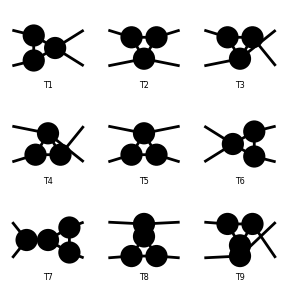

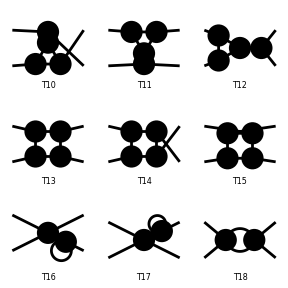

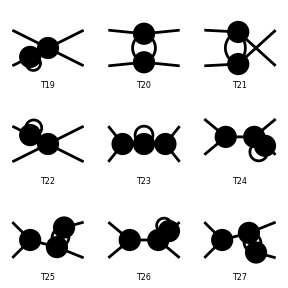

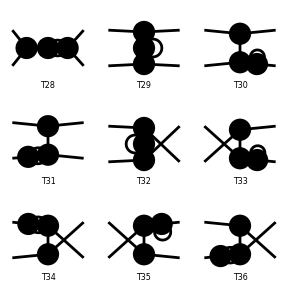

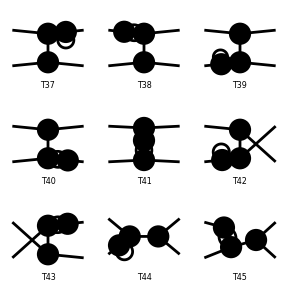

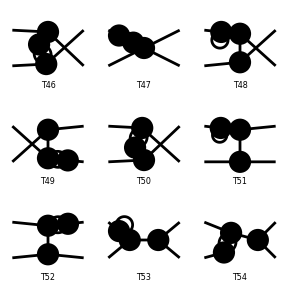

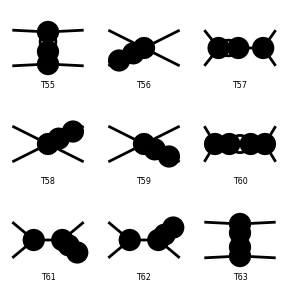

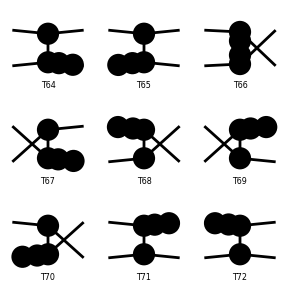

FeynArtsGraphics[2→2][([T1] | [T2] | [T3]
[T4] | [T5] | [T6]
[T7] | [T8] | [T9]),([T10] | [T11] | [T12]
[T13] | [T14] | [T15]
[T16] | [T17] | [T18]),([T19] | [T20] | [T21]
[T22] | [T23] | [T24]
[T25] | [T26] | [T27]),([T28] | [T29] | [T30]
[T31] | [T32] | [T33]
[T34] | [T35] | [T36]),([T37] | [T38] | [T39]
[T40] | [T41] | [T42]
[T43] | [T44] | [T45]),([T46] | [T47] | [T48]
[T49] | [T50] | [T51]
[T52] | [T53] | [T54]),([T55] | [T56] | [T57]
[T58] | [T59] | [T60]
[T61] | [T62] | [T63]),([T64] | [T65] | [T66]
[T67] | [T68] | [T69]
[T70] | [T71] | [T72]),([T73] | [T74] | Null
Null | Null | Null
Null | Null | Null)]

```mathematica
Paint[top]
```

```mathematica
Length[top]
```

74

```mathematica
Length[tops]
```

74

```mathematica
A = Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[4][7]],Propagator[Outgoing][Vertex[1][4],Vertex[4][7]],Propagator[Loop[1]][Vertex[3][5],Vertex[3][6]],Propagator[Loop[1]][Vertex[3][5],Vertex[4][7]],Propagator[Loop[1]][Vertex[3][6],Vertex[4][7]]];
```

> Top. 1 aebf/cgdg/efegfg.m, 0 diagrams

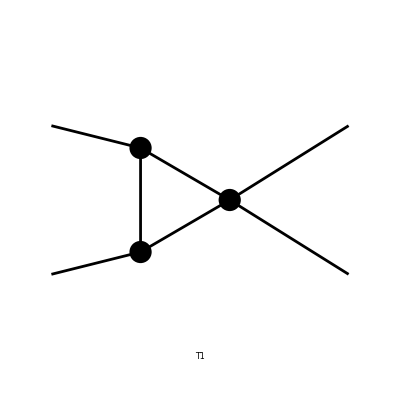

FeynArtsGraphics[2→2][([T1] | Null | Null
Null | Null | Null
Null | Null | Null)]

```mathematica
Paint[A]
```

> Top. 1 aebf/cgdf/egefgf.m, 0 diagrams

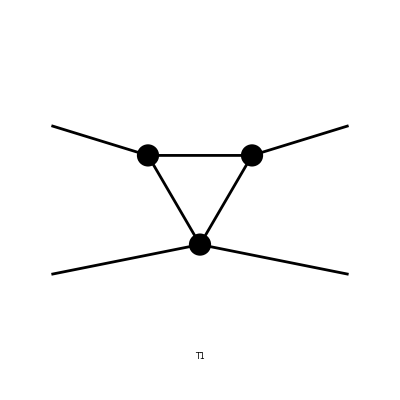

FeynArtsGraphics[2→2][([T1] | Null | Null
Null | Null | Null
Null | Null | Null)]

```mathematica
Paint[Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[4][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][7]],Propagator[Outgoing][Vertex[1][4],Vertex[4][6]],Propagator[Loop[1]][Vertex[3][5],Vertex[3][7]],Propagator[Loop[1]][Vertex[3][5],Vertex[4][6]],Propagator[Loop[1]][Vertex[3][7],Vertex[4][6]]]]
```

```mathematica
Paint[Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[4][5]],Propagator[Incoming][Vertex[1][2],Vertex[4][6]],Propagator[Outgoing][Vertex[1][3],Vertex[4][6]],Propagator[Outgoing][Vertex[1][4],Vertex[4][6]],Propagator[Internal][Vertex[4][5],Vertex[4][6]],Propagator[Loop[1]][Vertex[4][5],Vertex[4][5]]]]
```

> Top. 1 aebf/cfdf/efee.m, 0 diagrams

(*1) Load FeynArts and add the local model path*)
$ModelPath=Append[$ModelPath,/home/lev/Projects/calc_mbcwc/models];

(*2) Generate topologies:1-loop,2->2,only 4-point adjacencies,no tadpoles*)
tops=CreateTopologies[1,2->2,Adjacencies->{4},ExcludeTopologies->Tadpoles];

(*3) Insert fields from Phi4Matrix.mod*)
(*Phi4Matrix defines a single real scalar class S[1]*)
diags=InsertFields[tops,{S[1],S[1]}->{S[1],S[1]},Model->Phi4Matrix,InsertionLevel->{Classes}]

FeynArtsGraphics[2→2][([T1] | Null | Null
Null | Null | Null
Null | Null | Null)]

```mathematica
(*1) Load FeynArts and add the local model path*)
$ModelPath=Append[$ModelPath,"/home/lev/Projects/calc_mbcwc/models"];

(*2) Generate topologies:1-loop,2->2,only 4-point adjacencies,no tadpoles*)
tops=CreateTopologies[1,2->2,Adjacencies->{4},ExcludeTopologies->Tadpoles];
Format[Index[Colour,i_Integer]]:=SequenceForm["Cl1",i]
Format[Index[Colour2,i_Integer]]:=SequenceForm["Cl2",i]
(*3) Insert fields from Phi4Matrix.mod*)
(*Phi4Matrix defines a single real scalar class S[1]*)
diags=InsertFields[tops[[1]],{S[1],S[1]}->{S[1],S[1]},Model->"Phi4Matrix",InsertionLevel->{Classes}]
```

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

in total: 1 Classes insertion

TopologyList[Process→{S[1,{Cl11,Cl21,Tim1,RAx1}],S[1,{Cl12,Cl22,Tim2,RAx2}]}→{S[1,{Cl13,Cl23,Tim3,RAx3}],S[1,{Cl14,Cl24,Tim4,RAx4}]},Model→{Phi4Matrix},GenericModel→{Lorentz},InsertionLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[4][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[4][5],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[4][5],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[4][6],Field[4]],Propagator[Internal][Vertex[4][5],Vertex[4][6],Field[5]],Propagator[Loop[1]][Vertex[4][6],Vertex[4][6],Field[6]]]→Insertions[Generic][FeynmanGraph[2,Generic==1][Field[1]→S[1,{Cl11,Cl21,Tim1,RAx1}],Field[2]→S[1,{Cl12,Cl22,Tim2,RAx2}],Field[3]→S[1,{Cl13,Cl23,Tim3,RAx3}],Field[4]→S[1,{Cl14,Cl24,Tim4,RAx4}],Field[5]→S,Field[6]→S]→Insertions[Classes][FeynmanGraph[2,Classes==1][Field[1]→S[1,{Cl11,Cl21,Tim1,RAx1}],Field[2]→S[1,{Cl12,Cl22,Tim2,RAx2}],Field[3]→S[1,{Cl13,Cl23,Tim3,RAx3}],Field[4]→S[1,{Cl14,Cl24,Tim4,RAx4}],Field[5]→S[1,{Cl23,Cl11,Tim5,RAx5}],Field[6]→S[1,{Cl11,Cl14,Tim6,RAx6}]]]]]

> Top. 1 aebe/cedf/efff.m, 0 diagrams

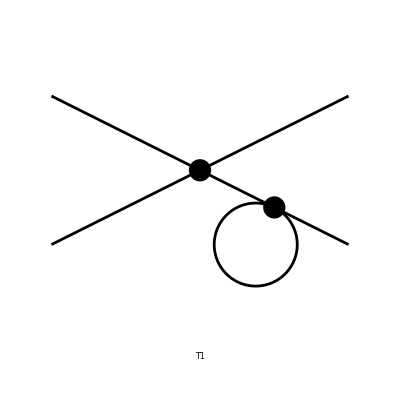

FeynArtsGraphics[2→2][([T1] | Null | Null
Null | Null | Null
Null | Null | Null)]

```mathematica
Paint[Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[4][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[4][5],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[4][5],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[4][6],Field[4]],Propagator[Internal][Vertex[4][5],Vertex[4][6],Field[5]],Propagator[Loop[1]][Vertex[4][6],Vertex[4][6],Field[6]]]]
```

> Top. 1 aebe/cfde/efff.m, 0 diagrams

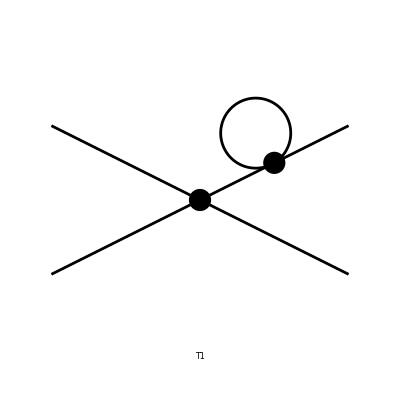

FeynArtsGraphics[2→2][([T1] | Null | Null
Null | Null | Null
Null | Null | Null)]

```mathematica
Paint[Topology[2][Propagator[Incoming][Vertex[1][1],Vertex[4][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[4][5],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[4][6],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[4][5],Field[4]],Propagator[Internal][Vertex[4][5],Vertex[4][6],Field[5]],Propagator[Loop[1]][Vertex[4][6],Vertex[4][6],Field[6]]]]
```